```mathematica
(*Для заданного порога ошибки ϵ∈(0,1) реализовать алгоритм вычисления сложности
аппроксимации в среднем n^avg(ϵ)*)
(*Задаем погор ошибки*)
ϵ=0.2;
(*Вводим данные, согласно условию*)
(*Невозрастающая последовательность собственных чисел ковариационного оператора*)
λ[k_]:=1/(π^2 k^2);
(*Соотвтетствующие собственным числам собственные функции*)
(*Subscript[Κψ, k]=Subscript[λ, k] Subscript[ψ, k]  k=1,2,...*)
ψ[k_, t_]:=√2 Cos[π k t];
(*Задем след ковариационного оператора*)
Λ=∑_(k=1)^(+∞) λ[k];
Print["Λ = ",N[ Λ]]
(*Алгоритм нахождения n^avg - сложности апроксимации в среднем*)
(*Задаем началььное значение для сложности апроксимации в среднем*)
navg=1;
(*Цикл с условием "пока"*)
While[∑_(k=1)^navg λ[k]<(1-ϵ^2)Λ,
 navg=navg+1;];
Print["При ϵ = ", ϵ]
Print["n^avg = ", navg]
```

Λ = 0.166667

При ϵ = 0.2

n^avg = 15

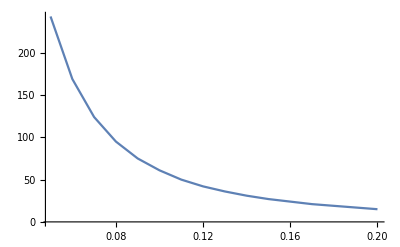

```mathematica
(*Построить график зависимости ϵ↦n^avg(ϵ)*)
(*Начальное значение порога ошибки*)
start = 0.2;
(*Конечное значение порога ошибки*)
end = 0.05;
(*Шаг изменения порога ошибки*)
step=0.01;
(*Список для хранения сложности
аппроксимации в среднем от заданного порога ошибки*)
navgs=List[];
(*Список для хранения порогов ошибки*)
errors=List[];
(*Начальное значение количества элементов в частичной сумме*)
n=0;
(*Начальное значение частичных сумм*)
PartAmount = 0;
(*Цикл по порогам ошибок*)
(*Первый порог ошибки равен start*)
(*Каждый последующий порог ошибки уменьшается на step*)
(*Пока порг ошибки не будет равен end*)
(*В данном случае частичная сумма не пересчитывается каждый раз, а учитывает прошлое значение*)
For[ϵ=start, ϵ ≥ end, ϵ = ϵ -step, 
(*Добавляем текущий порог ошибки в список порогов ошибок*)
AppendTo[errors,ϵ];
(*Пока частичная сумма по Subscript[λ, k] не станет больше либо равна (1-ϵ^2)*Λ*)

While[PartAmount < (1-ϵ^2)*Λ ,
n=n+1; (*Увеличиваем n на 1*)
PartAmount = PartAmount +λ[n]; (*Увеличиваем частичную сумму*)
];
(*Добавляем текущую сложности
аппроксимации в среднем в соответствующий список*)
AppendTo[navgs,n];
];
(*Строим графки зависимости сложности
аппроксимации в среднем от заданного порога ошибки*)
Print[ListLinePlot[Table[{errors[[i]],navgs[[i]]},{i,1,Length[navgs]}]]];
```

При n^avg = 16

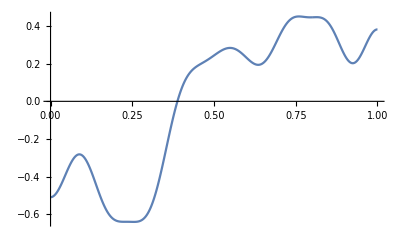

```mathematica
(*Для заданного порога ошибки ε∈(0,1) смоделировать процесс с помощью n^avg(ε)-ранговой частичной
суммы разложения Кархунена-Лоэва*)
(*Задаем погор ошибки*)
ϵ=0.195;
maxt=10000; (*Для разбиения отрезка [0,1] на равные интервалы*)
(*Так как у нас имеется список зависимостей n^avg(ϵ), то можно не всегда перебирать частичные суммы от 1*)
(*Если заданный порог ошибки ϵ^* больше, чем самый большой из списка, то частичные суммы будем считать от 1*)
If[ϵ> First[errors], start = 1;]
(*Цикл по всем элементам из списка порогов ошибок, кроме последнего*)
For[i=1, i < Length[errors], i++, 
(*Если заданный порог ошибок ϵ^* принадлежит лучу (ϵ[i+1], ϵ[i]], то частичные суммы будем считать от navgs[i]*)
If[errors[[i]]≥ ϵ && ϵ> errors[[i+1]],
 start = navgs[[i]];
];
];
(*Если заданный порог ошибки меньше, чем самый меньший из списка порогов ошибок, то частичные суммы будем считать от navgs[last]*)
If[ϵ ≤ Last[errors], start = Last[navgs];]
(*В качесте начального размера частичной суммы берем значение, найденое нами ранее*)
navg = start;
While[∑_(k=1)^navg λ[k]<(1-ϵ^2)Λ,
 navg=navg+1;];
(*Генерируем последовательность n случайных величин распределенных по нормальному закону*)
ξ=RandomVariate[NormalDistribution[0,1],navg];
(*Разложение Кархунена-Лоэва для заданного гауссовского процесса W^C(t)=W(t)-∫_0^1 W(s)ⅆs*)
W[t_]=∑_(k=1)^navg √λ[k]*ψ[k, t]*ξ[[k]];
Print["При n^avg = ",navg];
(*Составляем таблицу значений функции с шагом t в 1/maxt*)
Print[ListLinePlot[Table[{s/maxt,W[s/maxt]},{s,0,maxt}]]];
```